```mathematica
r1  = rb*{Cos[θ],Sin[θ],0}
```

```mathematica
{rb Cos[θ],rb Sin[θ],0}
```

{rb Cos[θ],rb Sin[θ],0}

```mathematica
disp = {-d,0,0}
```

{-d,0,0}

```mathematica
r1+disp
```

{-d+rb Cos[θ],rb Sin[θ],0}

```mathematica
Norm[r1-disp]^2
```

Abs[d+rb Cos[θ]]^2+Abs[rb Sin[θ]]^2

```mathematica
dist = (d+rb Cos[θ])^2+(rb Sin[θ])^2
```

(d+rb Cos[θ])^2+rb^2 Sin[θ]^2

```mathematica
Assuming[ {Element[θ,Reals],Cos[θ]<1, Sin[θ]>-1, Sin[θ]<1 , Cos[θ]>-1},Reduce[{dist>1.5^2/.rb->1.3,dist<1.7^2/.rb->1.3 },d,Reals]]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(-1.30769<Sin[θ]<-1.15385&&-1.3 Cos[θ]-0.1 √(289.-169. Sin[θ]^2)<d<-1.3 Cos[θ]+0.1 √(289.-169. Sin[θ]^2))||(-1.15385≤Sin[θ]≤1.15385&&(-1.3 Cos[θ]-0.1 √(289.-169. Sin[θ]^2)<d<-1.3 Cos[θ]-0.1 √(225.-169. Sin[θ]^2)||-1.3 Cos[θ]+0.1 √(225.-169. Sin[θ]^2)<d<-1.3 Cos[θ]+0.1 √(289.-169. Sin[θ]^2)))||(1.15385<Sin[θ]<1.30769&&-1.3 Cos[θ]-0.1 √(289.-169. Sin[θ]^2)<d<-1.3 Cos[θ]+0.1 √(289.-169. Sin[θ]^2))

```mathematica
Simplify[Abs[-d+rb Cos[θ]]^2+Abs[rb Sin[θ]]^2]
```

Abs[d-rb Cos[θ]]^2+Abs[rb Sin[θ]]^2

```mathematica
sol1 = 1.3 Cos[θ]-0.1 √(225.-169. Sin[θ]^2)
sol2 = 1.3 Cos[θ]+0.1 √(225.-169. Sin[θ]^2)
```

```mathematica
1.3 Cos[θ]-0.1 √(225.-169. Sin[θ]^2)
```

1.3 Cos[θ]-0.1 √(225.-169. Sin[θ]^2)

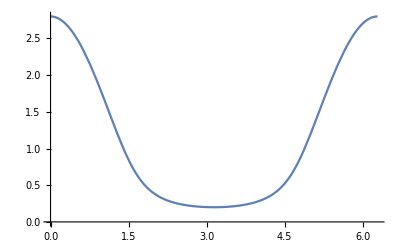

```mathematica
Plot[sol2,{θ,0,2 π}]
```

```mathematica
dist/.d->sol2/.θ->0/.rb->1.3
```

2.25

```mathematica
lower1 = -1.3 Cos[θ]-0.1 √(289.-169. Sin[θ]^2)
lower2 = -1.3 Cos[θ]+0.1 √(225.-169. Sin[θ]^2)
```

-1.3 Cos[θ]-0.1 √(289.-169. Sin[θ]^2)

-1.3 Cos[θ]+0.1 √(225.-169. Sin[θ]^2)

```mathematica
upper1 = -1.3 Cos[θ]-0.1 √(225.-169. Sin[θ]^2)
upper2 =-1.3 Cos[θ]+0.1 √(16*16.-169. Sin[θ]^2)
```

-1.3 Cos[θ]-0.1 √(225.-169. Sin[θ]^2)

-1.3 Cos[θ]+0.1 √(256.-169. Sin[θ]^2)

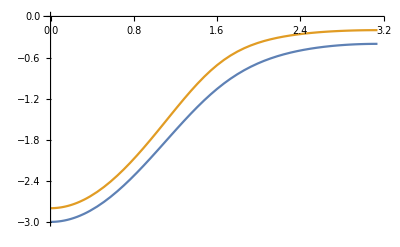

```mathematica
Plot[{lower1,upper1}, {θ,0,Pi} ]
```

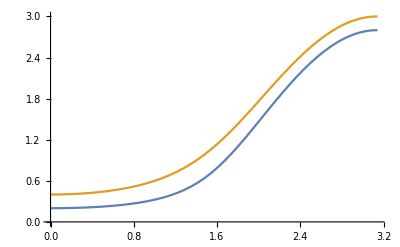

```mathematica
Plot[{lower2,upper2}, {θ,0,Pi} ]
```

```mathematica
lower2/.θ->0
```

0.2

```mathematica
lower2/.θ->Pi/4
```

0.266088

```mathematica
lower2/.θ->Pi
```

2.8

```mathematica
lower2
```

-1.3 Cos[θ]+0.1 √(225.-169. Sin[θ]^2)

```mathematica
Norm[separation/.rb->1.3/.d->lower2/.θ->Pi/2]
Norm[separation/.rb->1.3/.d->upper2/.θ->Pi/2]
```

1.5

1.7

```mathematica
upper2
```

-1.3 Cos[θ]+0.1 √(256.-169. Sin[θ]^2)

```mathematica
lower2
```

-1.3 Cos[θ]+0.1 √(225.-169. Sin[θ]^2)

```mathematica
placement =(lower2+upper2)/2
```

1/2 (-2.6 Cos[θ]+0.1 √(225.-169. Sin[θ]^2)+0.1 √(256.-169. Sin[θ]^2))

```mathematica
1/2 (-2.6 Cos[θ]+0.1 √(225.-169. Sin[θ]^2)+0.1 √(.-169. Sin[θ]^2))
```

```mathematica
placement/.θ->Pi/2
```

0.840535

```mathematica
separation  = r1-disp
```

{d+rb Cos[θ],rb Sin[θ],0}

```mathematica
separation/.rb->1.3/. d->lower2
```

{0.+0.1 √(225.-169. Sin[θ]^2),1.3 Sin[θ],0}